# Hw 6 - Complex Variables

## Page 237 visualize curvature

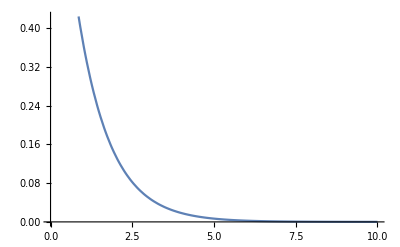

```mathematica
Plot[E^-x,{x,0,10}]
```

## 3 ii - done using calculations

### First assign Φ to the expression

```mathematica
Clear[Φ]
Φ=E^(x^2-y^2)Cos[2x y]
```

ⅇ^(x^2-y^2) Cos[2 x y]

### Add together the second partial derivatives

```mathematica
D[Φ,{x,2}]+D[Φ,{y,2}]
```

-4 ⅇ^(x^2-y^2) x^2 Cos[2 x y]+(2 ⅇ^(x^2-y^2)+4 ⅇ^(x^2-y^2) x^2) Cos[2 x y]-4 ⅇ^(x^2-y^2) y^2 Cos[2 x y]+(-2 ⅇ^(x^2-y^2)+4 ⅇ^(x^2-y^2) y^2) Cos[2 x y]

### Simplify the previous output. In this case, it simplifies to zero.

```mathematica
Simplify[%]
```

0

## 5 computational

### Here we define Cauchy-Riemann equations

```mathematica
cauchyRiemannCartCart[u_,v_]:=Module[{ux,uy,vx,vy},
ux=D[u,x];
uy=D[u,y];
vx=D[v,x];
vy=D[v,y];
Return[ux==vy&&vx==-uy]
]
```

```mathematica
cauchyRiemannPolarCart[u_,v_,r_]:=Module[{uθ,ur,vθ,vr},
uθ=D[u,θ];
ur=D[u,r];
vθ=D[v,θ];
vr=D[v,r];
Return[uθ==r ur&&uθ==-r vr]
]
```

### i) f==ⅇ^-y (cos(x)+ⅈ sin(x))

```mathematica
Clear[f,u,v]
f=ⅇ^-y(Cos[x]+ⅈ Sin[x]);
u=FullSimplify[Re[f],Element[{x,y},Reals]]
v=FullSimplify[Im[f],Element[{x,y},Reals]]
```

ⅇ^-y Cos[x]

ⅇ^-y Sin[x]

```mathematica
FullSimplify[cauchyRiemannCartCart[u,v],Element[{x,y},Reals]]
```

True

#### f==ⅇ^-y (cos(x)+ⅈ sin(x)) is analytic

### ii) f==cos(x)-ⅈ sin(y)

```mathematica
Clear[f,u,v]
f=Cos[x]-ⅈ Sin[y];
u=FullSimplify[Re[f],Element[{x,y},Reals]]
v=FullSimplify[Im[f],Element[{x,y},Reals]]
```

Cos[x]

-Sin[y]

```mathematica
FullSimplify[cauchyRiemannCartCart[u,v],Element[{x,y},Reals]]
```

Cos[y]==Sin[x]

#### f==cos(x)-ⅈ sin(y) is not analytic

### iii) f=r^3+ⅈ 3 θ

```mathematica
Clear[f,u,v,r]
f=r^3+ⅈ 3 θ;
u=FullSimplify[Re[f],Element[{r,θ},Reals]]
v=FullSimplify[Im[f],Element[{r,θ},Reals]]
r$length=Norm[f,Element[{r,θ},Reals]]
```

r^3

3 θ

Norm[r^3+3 ⅈ θ,(r|θ)∈Reals]

```mathematica
FullSimplify[cauchyRiemannPolarCart[u,v,r$length],Element[{u,v,r$length},Reals]]
```

True

#### f=r^3+ⅈ 3 θ is analytic

### iv) f==r ⅇ^(r cos(θ)+ⅈ (θ+r cos(θ)))

#### Here I had to split up the function into two parts to make Mathematica evaluate it correctly

```mathematica
Clear[f,u,v,r]
f=ⅇ^(ⅈ(θ+r Cos[θ]))
u=r ⅇ^(r Cos[θ])FullSimplify[Re[f],Element[{r,θ},Reals]]
v=r ⅇ^(r Cos[θ])FullSimplify[Im[f],Element[{r,θ},Reals]]
r$length=Norm[r ⅇ^(r Cos[θ])f,Element[{r,θ},Reals]]
```

ⅇ^(ⅈ (θ+r Cos[θ]))

ⅇ^(r Cos[θ]) r Cos[θ+r Cos[θ]]

ⅇ^(r Cos[θ]) r Sin[θ+r Cos[θ]]

Norm[ⅇ^(r Cos[θ]+ⅈ (θ+r Cos[θ])) r,(r|θ)∈Reals]

```mathematica
FullSimplify[cauchyRiemannPolarCart[u,v,r$length],Element[{u,v,r$length},Reals]]
```

r (r Cos[θ+r Cos[θ]] Sin[θ]+(1-r Sin[θ]) Sin[θ+r Cos[θ]])==0

#### f==r ⅇ^(r cos(θ)+ⅈ (θ+r cos(θ))) is not analytic